FittedModel[1023.8/(1+39.9993 ⅇ^(-0.352139 x))]

0.999611

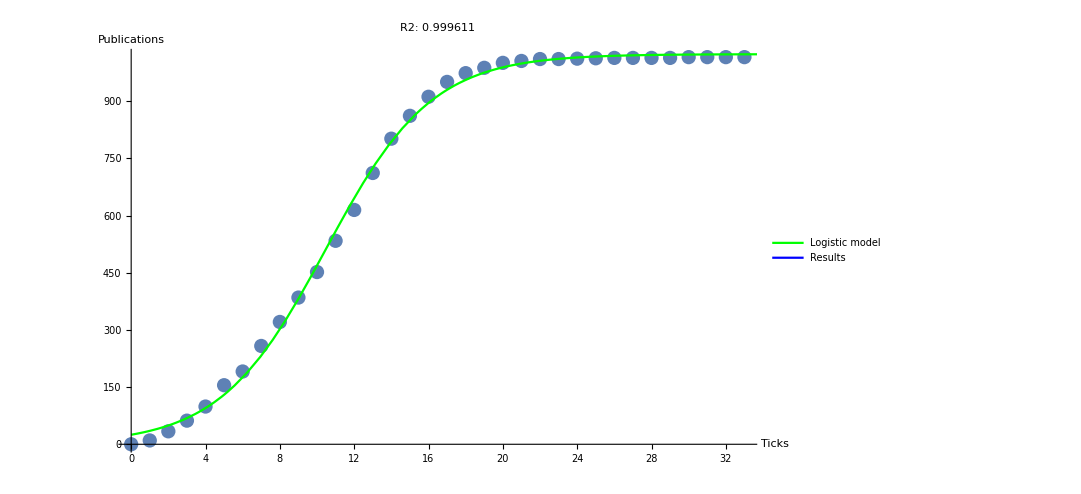

```mathematica
dataPublicationsCurve = Import["/home/fabianact/newTest/ModeloConAcumulaciondoble/test0/testTables/publications15-1-1-curve.csv"];
fitFkt=NonlinearModelFit[dataPublicationsCurve,c/(1+a Exp[-b x]),{a,b,c},x]
fitFkt[{"BestFit","ParameterTable"}];
R2=fitFkt["AdjustedRSquared"]
plot=Show[ListPlot[dataPublicationsCurve,ImageSize->800,AxesLabel->{"Ticks","Publications"}, PlotLabel->"R2: " <> ToString[R2]],Plot[fitFkt[x],{x,0,Length[dataPublicationsCurve]},  PlotStyle->Green]];
plotTotal = Legended[plot,LineLegend[{Green,Blue},{"Logistic model","Results"}]]
Export["fitLogistic.png",plotTotal];
```